```mathematica
<<"C:/users/julian/documents/github/Machine-Vision/MVTools.m"
```

```mathematica
lfw=Map[StandardiseImage[Import[#],32]&,FileNames["C:\\Users\\Julian\\Downloads\\lfwcrop_grey\\lfwcrop_grey\\faces\\c*.pgm"]];Length[lfw]
```

902

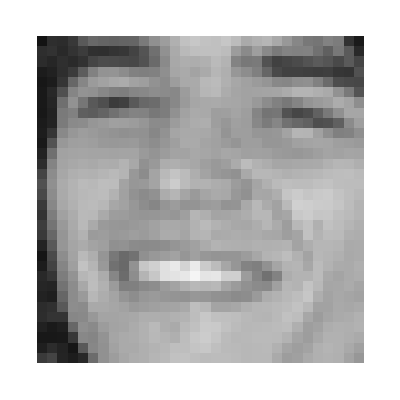

```mathematica
{lfw[[2]]//DispImage}
```

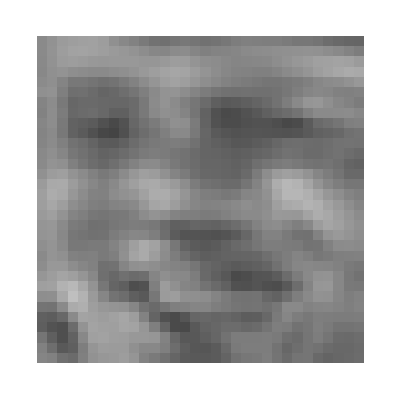
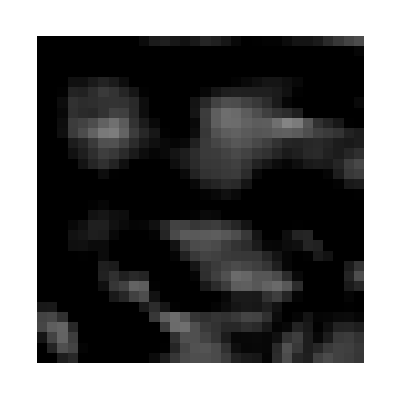

```mathematica
{MVCorrelateImage[lfw[[1]],rightEye,NormalizedSquaredEuclideanDistance]//DispImage,
MVCorrelateImage[lfw[[1]],rightEye,Correlation]//DispImage}
```

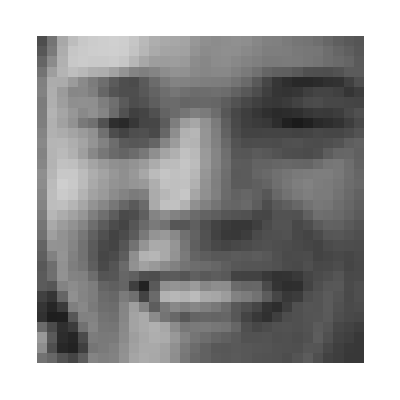

```mathematica
{lfw[[1]]//ObjectRecognitionOutput}
```